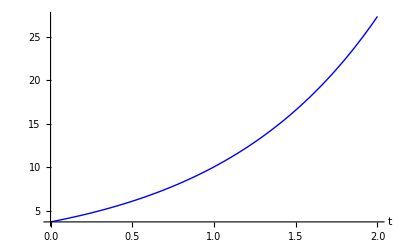

```mathematica
y[x_]:=Cosh[x^2]
Plot[y[√(t+2)],{t,0,2},AxesLabel->Automatic,PlotStyle->{Blue,Thick}]
```

```mathematica
res=Solve[{-b+2a==5,-6 a+17 b+2 c==18,-21 a+15 c==3}]
vyr=a+b-c
N[vyr/.res]
```

{{a→513/154,b→128/77,c→107/22}}

a+b-c

{0.12987}

```mathematica
soustavaRovnic={3f'[t]+2g[t]==-E/10*f[t],5f[t]-g'[t]==0}
soustavaPodminek={f[0]==0,g[0]==1}
```

{2 g[t]+3 f'[t]==-1/10 ⅇ f[t],5 f[t]-g'[t]==0}

{f[0]==0,g[0]==1}

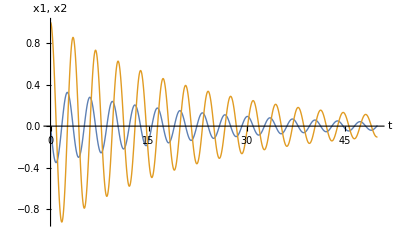

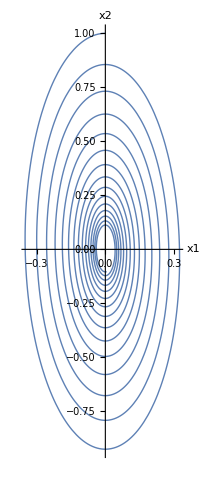

```mathematica
rovniceVsechny=Union[soustavaRovnic,soustavaPodminek];
neznameDif={f[t],g[t]};
tmax=50;
reseniDif=NDSolve[rovniceVsechny,neznameDif,{t,0,tmax}];
Plot[Evaluate[neznameDif/.reseniDif],{t,0,tmax},AxesLabel->{"t", "x1, x2"},PlotStyle->Thick,PlotRange->All]
ParametricPlot[Evaluate[neznameDif/.reseniDif],{t,0,tmax},AxesLabel->{"x1","x2"},PlotStyle->Thick,PlotRange->All]
```